```mathematica
PacletDirectoryLoad[]
Needs["Wolfram`TensorNetworks`"]
```

{/Users/mohammadb/Documents/GitHub/TensorNetworks/}

## Playground

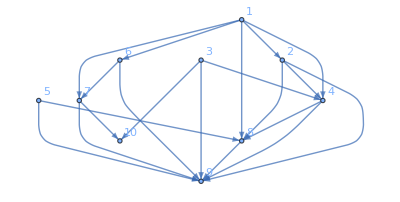

```mathematica
net=ToTensorNetworkGraph[RandomGraph[{10,20}],Method->"RandomComplex"]
```

```mathematica
tn=TensorNetwork@net
```

TensorNetwork[…]

```mathematica
TensorNetworkContract[net]//AbsoluteTiming
```

{0.007676,4.37334+24.6301 ⅈ}

```mathematica
TensorNetworkContract[tn]//AbsoluteTiming
```

{0.006688,4.37334+24.6301 ⅈ}

```mathematica
TensorNetworkContract[net,Method->"Naive"]//AbsoluteTiming
```

{0.005028,4.37334+24.6301 ⅈ}

methods
 “Optimal”,”flops” ,“max” | “size” | “write” | “combo” | “limit”

```mathematica
TensorNetworkFindContractionPath[net]
```

{{3,9},{6,9},{3,4},{5,7},{5,6},{3,5},{2,4},{2,3},{1,2}}

```mathematica
TensorNetworkFindContractionPath[net,Method->"size"]
```

{{3,9},{6,9},{3,4},{5,7},{5,6},{3,5},{2,4},{2,3},{1,2}}

```mathematica
path=TensorNetworkFindContractionPath[net,Method->"max"]
```

{{5,6},{2,9},{7,8},{3,7},{2,6},{2,5},{3,4},{2,3},{1,2}}

```mathematica
Activate/@AssociationMap[TensorNetworkContraction[net,path,Method->#]&,$TensorNetworkContractionMethods]
```

<|ArrayDotTranspose→-13.8364-46.3534 ⅈ,ArrayDot→-13.8364-46.3534 ⅈ,Dot→-13.8364-46.3534 ⅈ,TensorContract→-13.8364-46.3534 ⅈ,TableSum→-13.8364-46.3534 ⅈ|>

```mathematica
tn=TensorNetwork[{{1,2,3},{4,2,3},{1,5}}]
```

TensorNetwork[…]

```mathematica
tn["Hypergraph"]
```

-Graphics-

```mathematica
BinaryTensorNetworkQ@tn
```

True